# BKM10 Mathematica Notebook:

## A notebook for testing the BKM10 coefficients and code. Written by Dima Watkins [bem8mq@virginia.edu]

```mathematica
$MachinePrecision
```

15.9546

## (#0): Good Mathematica Practice:

```mathematica
ClearAll["Global`*"];
```

## (#1): Static Quantities:

```mathematica
MassOfProton=Quantity[.93827208816,"Gigaelectronvolts"];
ElectricFormFactorConstant=Quantity[0.710649,"Gigaelectronvolts Squared"];
ElectromagneticFineStructureConstant=1/137.035999177;
ProtonMagneticMoment=2.79284734463;
```

```mathematica
qSquared=Quantity[1.8200000524520876,"Gigaelectronvolts Squared"];
xB=0.3429999947547912;
t=Quantity[-0.1720000058412552,"Gigaelectronvolts Squared"];
k=Quantity[5.75,"Gigaelectronvolts"];
```

```mathematica
Realℋ=-0.897;
RealℋT=2.444;
Realℰ=-0.541;
RealℰT=2.207;
Imaginaryℋ=2.421;
ImaginaryℋT=1.131;
Imaginaryℰ=0.903;
ImaginaryℰT=5.383;
ℋ=Realℋ+I Imaginaryℋ;
ℋT=RealℋT+I ImaginaryℋT;
ℰ=Realℰ+I Imaginaryℰ;
ℰT=RealℰT+I ImaginaryℰT;
```

```mathematica
LeptonλUnpolarizedBeam=0;
LeptonλPlus=1/2;
LeptonλMinus=-1/2;
unpolarizedTargetΛ=0;
lpTargetΛ=1;
```

```mathematica
ConvertGeVMinus6ToNbGevMinus4[ValueInGeVMinus6_]:=Quantity[.389379*1000000*ValueInGeVMinus6,("Nanobarns"*"Gigaelectronvolts"*"Gigaelectronvolts")];
```

## (#2): Derived Quantities:

## (#2.1.1): Derived Kinematics | ϵ

```mathematica
Epsilon[qSquared_,xB_]:=2xB(MassOfProton/(√qSquared));
ϵ=Epsilon[qSquared,xB]
```

0.477109

```mathematica
ϵ^2
```

0.227633

## (#2.1.2): Derived Kinematics | y

```mathematica
LeptonEnergyFraction[qSquared_,k_,ϵ_]:=(√qSquared)/(ϵ k);
```

```mathematica
y=LeptonEnergyFraction[qSquared,k,ϵ]
```

0.491757

## (#2.1.3): Derived Kinematics | ξ

```mathematica
SkewnessParameter[qSquared_,xB_,t_]:=xB((1+t/(2*qSquared))/(2-xB+(xB t)/qSquared));
ξ=SkewnessParameter[qSquared,xB,t]
```

0.201154

## (#2.1.4): Derived Kinematics | t_min

```mathematica
tMinimum[qSquared_,xB_,ϵ_]:=-qSquared*((2(1-xB)(1 - √(1 + ϵ^2)) + ϵ^2)/(4 xB (1-xB)+ ϵ^2));
tMin=tMinimum[qSquared,xB,ϵ]
```

-0.138211 GeV^2

## (#2.1.5): Derived Kinematics | t'

```mathematica
tPrime[t_,tMinimum_]:=t-tMinimum;
tP=tPrime[t,tMin]
```

-0.0337889 GeV^2

## (#2.1.6): Derived Kinematics | K̃

```mathematica
kTilde[qSquared_,xB_,y_,t_,ϵ_,tMin_]:=√(tMin-t)√((1-xB)√(1+ϵ^2)+((tMin-t)(ϵ^2+4(1-xB)xB))/(4qSquared));
kT=kTilde[qSquared,xB,y,t,ϵ,tMin]
```

0.157396 GeV

## (#2.1.7): Derived Kinematics | K

```mathematica
KinematicK[qSquared_,y_,ϵ_,kTilde_]:=kTilde√((1-y+(ϵ^2 y^2)/4)/qSquared);
K=KinematicK[qSquared,y,ϵ,kT]
```

0.0842939

## (#2.2.1): Derived Form Factors | F_E

```mathematica
ElectricFormFactor[t_]:=1/(1-t/ElectricFormFactorConstant)^2;
FE=ElectricFormFactor[t]
```

0.648238

## (#2.2.2): Derived Form Factors | F_G

```mathematica
MagneticFormFactor[FE_]:=ProtonMagneticMoment*FE;
FG=MagneticFormFactor[0.6482376115457034]
```

1.81043

## (#2.2.3): Derived Form Factors | F_2

```mathematica
PauliFormFactor[t_,FElectric_,FMagnetic_]:=(FMagnetic-FElectric)/(1+(-t)/(4 MassOfProton^2));
F2=PauliFormFactor[t,FE,FG]
```

1.10807

## (#2.2.4): Derived Form Factors | F_1

```mathematica
DiracFormFactor[t_,FMagnetic_,F2Pauli_]:=FMagnetic-F2Pauli;
F1=DiracFormFactor[t,FG,F2]
```

0.70236

## (#2.2.5): Derived Form Factors | ℱ_eff

```mathematica
EffectiveFormFactor[ξ_,ℱ_]:=-2ξ ℱ(1/(1+ξ));
EffectiveFormFactor[ξ,Realℋ]
EffectiveFormFactor[ξ,RealℋT]
EffectiveFormFactor[ξ,Realℰ]
EffectiveFormFactor[ξ,RealℰT]
EffectiveFormFactor[ξ,Imaginaryℋ]
EffectiveFormFactor[ξ,ImaginaryℋT]
EffectiveFormFactor[ξ,Imaginaryℰ]
EffectiveFormFactor[ξ,ImaginaryℰT]
```

0.300437

-0.818581

0.1812

-0.739202

-0.810878

-0.378812

-0.302446

-1.80296

## (#3.1): Unpolarized Target:

### (#3.1.1): (C^unp)_(++)(n=0):

```mathematica
CunpPP0[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=-((4(2-y)(1+√(1+ϵ^2)))/(1+ϵ^2)^2)((KTilde^2/qSquared)((2-y)^2/(√(1+ϵ^2)))+(t/qSquared)(1-y-(ϵ^2/4)y^2)(2-xB)(1+((2xB(2-xB+(√(1+ϵ^2)-1)/2+ϵ^2/(2xB))(t/qSquared)+ϵ)/((2-xB)(1+√(1+ϵ^2))))^2));

CunpPP0[qSquared,xB,t,ϵ,y,kT]
```

0.423957

### (#3.1.2): (C^(unp, V))_(++)(n=0):

```mathematica
CunpVPP0[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((8(2-y))/(1+ϵ^2)^2)((xB t)/qSquared)(((2-y)^2 KTilde^2)/(√(1+ϵ^2)qSquared)+(1-y-(ϵ^2/4)y^2)((1+√(1+ϵ^2))/2)(1+t/qSquared)(1+((√(1+ϵ^2)-1+2xB)/(1+√(1+ϵ^2)))(t/qSquared)));

CunpVPP0[qSquared,xB,t,ϵ,y,kT]
```

-0.125368

### (#3.1.3): (C^(unp, A))_(++)(n=0):

```mathematica
CunpAPP0[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((8(2-y))/(1+ϵ^2)^2)( t/qSquared)((((2-y)^2 KTilde^2)/(√(1+ϵ^2)qSquared))((1+√(1+ϵ^2)-2xB)/2)+(1-y-(ϵ^2/4)y^2)(((1+√(1+ϵ^2))/2)(1+√(1+ϵ^2)-xB+(√(1+ϵ^2)-1+xB(( 3+√(1+ϵ^2)-2xB)/(1+√(1+ϵ^2))))(t/qSquared)))-2(KTilde^2/qSquared));

CunpAPP0[qSquared,xB,t,ϵ,y,kT]
```

-0.665662

### (#3.1.4): (C^unp)_(++)(n=1):

```mathematica
CunpPP1[qSquared_,xB_,t_,ϵ_,y_,K_]:=((-16 K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((1+(1-xB)((√(ϵ^2+1)-1)/(2xB))+ϵ^2/(4xB))((xB t)/qSquared)-(3 ϵ^2)/4)-4K(2-2y+y^2+(ϵ^2/2)y^2)((1+√(1+ϵ^2)-ϵ^2)/(1+ϵ^2)^(5/2))(1-(1-3xB)(t/qSquared)+((1-√(1+ϵ^2)+3 ϵ^2)/(1+√(1+ϵ^2)-ϵ^2))((xB t)/qSquared));

CunpPP1[qSquared,xB,t,ϵ,y,K]
```

-0.397418

### (#3.1.5): (C^(unp, V))_(++)(n=1):

```mathematica
CunpVPP1[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((16K)/(1+ϵ^2)^(5/2))((xB t)/qSquared)((2-y)^2(1-(1-2xB)(t/qSquared))+(1-y-(ϵ^2/4)y^2)((1+√(1+ϵ^2)-2xB)/2)(tPrime/qSquared));
CunpVPP1[qSquared,xB,t,ϵ,y,tP,K]
```

-0.0611543

### (#3.1.6): (C^(unp, A))_(++)(n=1):

```mathematica
CunpAPP1[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((-16K)/(1+ϵ^2)^2)( t/qSquared)((1-y-(ϵ^2/4)y^2)(1-(1-2xB)(t/qSquared)+((4xB(1-xB)+ϵ^2)/(4√(1+ϵ^2)))(tPrime/qSquared))-(2-y)^2(1-xB/2+((1+√(1+ϵ^2)-2xB)/4)(1-t/qSquared)+((4xB(1-xB)+ϵ^2)/(2√(1+ϵ^2)))(tPrime/qSquared)));
CunpAPP1[qSquared,xB,t,ϵ,y,tP,K]
```

-0.189568

### (#3.1.7): (C^unp)_(++)(n=2):

```mathematica
CunpPP2[qSquared_,xB_,t_,ϵ_,y_,tPrime_,KTilde_]:=((8(2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)(((2 ϵ^2)/(√(1+ϵ^2)(1+√(1+ϵ^2))))(KTilde^2/qSquared)+((xB t tPrime)/qSquared^2)(1-xB-(√(1+ϵ^2)-1)/2+ϵ^2/(2xB)));

CunpPP2[qSquared,xB,t,ϵ,y,tP,kT]
```

0.0127312

### (#3.1.8): (C^(unp,V))_(++)(n=2):

```mathematica
CunpVPP2[qSquared_,xB_,t_,ϵ_,y_,tPrime_,KTilde_]:=((8(2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)((xB t)/qSquared)((4 KTilde^2)/(√(1+ϵ^2)qSquared)+((1+√(1+ϵ^2)-2xB)/2)(1+t/qSquared)(tPrime/qSquared));
CunpVPP2[qSquared,xB,t,ϵ,y,tP,kT]
```

-0.00477238

### (#3.1.9): (C^(unp,A))_(++)(n=2):

```mathematica
CunpAPP2[qSquared_,xB_,t_,ϵ_,y_,tPrime_,KTilde_]:=((4(2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)( t/qSquared)((4 (1-2xB)KTilde^2)/(√(1+ϵ^2)qSquared)-(3-√(1+ϵ^2)-2xB+ϵ^2/xB)((xB tPrime)/qSquared));
CunpAPP2[qSquared,xB,t,ϵ,y,tP,kT]
```

-0.00511373

### (#3.1.10): (C^unp)_(++)(n=3):

```mathematica
CunpPP3[qSquared_,xB_,t_,ϵ_,y_,K_]:=-8K(1-y-(ϵ^2/4)y^2)((√(1+ϵ^2)-1)/(1+ϵ^2)^(5/2))((1-xB)(t/qSquared)+((√(1+ϵ^2)-1)/2)(1+t/qSquared));

CunpPP3[qSquared,xB,t,ϵ,y,K]
```

0.000284642

### (#3.1.11): (C^(unp, V))_(++)(n=3):

```mathematica
CunpVPP3[qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared));
CunpVPP3[qSquared,xB,t,ϵ,y,K]
```

-0.000170889

### (#3.1.12): (C^(unp, A))_(++)(n=3):

```mathematica
CunpAPP3[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((16K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((t tPrime)/qSquared^2)(xB(1-xB)+ϵ^2/4);
CunpAPP3[qSquared,xB,t,ϵ,y,tP,K]
```

0.000197789

### (#3.1.13): (C^unp)_(0+)(n=0):

```mathematica
Cunp0P0[qSquared_,xB_,t_,ϵ_,y_,K_]:=((12√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(ϵ^2+((2-6xB-ϵ^2)/3)(t/qSquared));

Cunp0P0[qSquared,xB,t,ϵ,y,K]
```

0.215

### (#3.1.14): (C^(unp,V))_(0+)(n=0):

```mathematica
Cunp0P0V[qSquared_,xB_,t_,ϵ_,y_,K_]:=((24√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1-(1-2xB)(t/qSquared));

Cunp0P0V[qSquared,xB,t,ϵ,y,K]
```

-0.0606525

### (#3.1.15): (C^(unp,A))_(0+)(n=0):

```mathematica
Cunp0P0A[qSquared_,xB_,t_,ϵ_,y_,K_]:=((4√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))( t/qSquared)(8-6xB+5 ϵ^2)(1-(t/qSquared)((2-12xB(1-xB)-ϵ^2)/(8-6xB+5 ϵ^2)));

Cunp0P0A[qSquared,xB,t,ϵ,y,K]
```

-0.200129

### (#3.1.16): (C^unp)_(0+)(n=1):

```mathematica
Cunp0P1[qSquared_,xB_,t_,ϵ_,y_,tPrime_]:=((8√2√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)((2-y)^2(tPrime/qSquared)(1-xB+(((1-xB)xB+ϵ^2/4)/(√(1+ϵ^2)))(tPrime/qSquared))+((1-y-(ϵ^2/4)y^2)/(√(1+ϵ^2)))(1-(1-2xB)(t/qSquared))(ϵ^2-2(1+ϵ^2/(2xB))((xB t)/qSquared)));

Cunp0P1[qSquared,xB,t,ϵ,y,tP]
```

0.616232

### (#3.1.17): (C^(unp,V))_(0+)(n=1):

```mathematica
Cunp0P1V[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((16√2√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)((KTilde^2(2-y)^2)/qSquared+(1-(1-2xB)(t/qSquared))^2(1-y-(ϵ^2/4)y^2));

Cunp0P1V[qSquared,xB,t,ϵ,y,kT]
```

-0.171499

### (#3.1.18): (C^(unp,A))_(0+)(n=1):

```mathematica
Cunp0P1A[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((8√2√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))( t/qSquared)((KTilde^2/qSquared)(1-2xB)(2-y)^2+(1-(1-2xB)(t/qSquared))(1-y-(y^2 ϵ^2)/4)(4-2xB+3 ϵ^2+(t/qSquared)(4xB(1-xB)+ϵ^2)));

Cunp0P1A[qSquared,xB,t,ϵ,y,kT]
```

-0.896218

### (#3.1.19): (C^unp)_(0+)(n=2):

```mathematica
Cunp0P2[qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(1+ϵ^2/2)(1+((1+ϵ^2/(2xB))/(1+ϵ^2/2))((xB t)/qSquared));

Cunp0P2[qSquared,xB,t,ϵ,y,K]
```

-0.648517

### (#3.1.20): (C^(unp,V))_(0+)(n=2):

```mathematica
Cunp0P2V[qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1+(1-2xB)(t/qSquared));

Cunp0P2V[qSquared,xB,t,ϵ,y,K]
```

-0.0190522

### (#3.1.20): (C^(unp,A))_(0+)(n=2):

```mathematica
Cunp0P2A[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((8√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)( t/qSquared)(1-xB+(tPrime/(2qSquared))((4xB(1-xB)+ϵ^2)/(√(1+ϵ^2))));

Cunp0P2A[qSquared,xB,t,ϵ,y,tP,K]
```

-0.0410709

### (#3.1.21): (S^unp)_(++)(n=1):

```mathematica
SunpPP1[λ_,qSquared_,xB_,ϵ_,y_,tPrime_,K_]:=((8λ K(2-y)y)/(1+ϵ^2))(1+((1-xB+(√(1+ϵ^2)-1)/2)/(1+ϵ^2))(tPrime/qSquared));
SunpPP1[LeptonλPlus,qSquared,xB,ϵ,y,tP,K]
```

0.201518

### (#3.1.22): (S^(unp,V))_(++)(n=1):

```mathematica
SunpPP1V[λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8λ K(2-y)y)/(1+ϵ^2)^2)((xB t)/qSquared)(√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared));
SunpPP1V[LeptonλPlus,qSquared,xB,t,ϵ,y,K]
```

-0.000142001

### (#3.1.23): (S^(unp,A))_(++)(n=1):

```mathematica
SunpPP1A[λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((8λ K(2-y)y)/(1+ϵ^2))( t/qSquared)(1+(1-2xB)((1+√(1+ϵ^2)-2xB)/(2√(1+ϵ^2)))(tPrime/qSquared));
SunpPP1A[LeptonλPlus,qSquared,xB,t,ϵ,y,tP,K]
```

-0.0191796

### (#3.1.24): (S^unp)_(++)(n=2):

```mathematica
SunpPP2[λ_,qSquared_,xB_,ϵ_,y_,tPrime_]:=-((4λ(1-y-(ϵ^2/4)y^2)y)/(1+ϵ^2)^(3/2))(1+√(1+ϵ^2)-2xB)(tPrime/qSquared)((ϵ^2-xB(√(1+ϵ^2)-1))/(1+√(ϵ^2+1)-2xB)-((2xB+ϵ^2)/(2√(1+ϵ^2)))(tPrime/qSquared));
SunpPP2[LeptonλPlus,qSquared,xB,ϵ,y,tP]
```

0.00133739

### (#3.1.25): (S^(unp,V))_(++)(n=2):

```mathematica
SunpPP2V[λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4λ(1-y-(ϵ^2/4)y^2)y)/(1+ϵ^2)^2)((xB t)/qSquared)(1-(1-2xB)(t/qSquared))(√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared));
SunpPP2V[LeptonλPlus,qSquared,xB,t,ϵ,y]
```

-0.000284343

### (#3.1.26): (S^(unp,A))_(++)(n=2):

```mathematica
SunpPP2A[λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_]:=-((8λ (1-y-(ϵ^2/4)y^2)y)/(1+ϵ^2)^2)(( t tPrime)/qSquared^2)(1+√(1+ϵ^2)-2xB)(1+((4(1-xB)xB+ϵ^2)/(4-2xB+3 ϵ^2))(t/qSquared));
SunpPP2A[LeptonλPlus,qSquared,xB,t,ϵ,y,tP]
```

-0.00156721

### (#3.1.27): (S^unp)_(0+)(n=1):

```mathematica
Sunp0P1[λ_,qSquared_,ϵ_,y_,kTilde_]:=((8λ √2(2-y)y√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)(kTilde^2/qSquared);
Sunp0P1[LeptonλPlus,qSquared,ϵ,y,kT]
```

0.0266473

### (#3.1.28): (S^(unp,V))_(0+)(n=1):

```mathematica
Sunp0P1V[λ_,qSquared_,xB_,t_,ϵ_,y_]:=((4√2λ y (2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)((xB t)/qSquared)(4(1-2xB)(t/qSquared)(1+(xB t)/qSquared)+ϵ^2(1+t/qSquared)^2);
Sunp0P1V[LeptonλPlus,qSquared,xB,t,ϵ,y]
```

-0.0022778

### (#3.1.29): (S^(unp,A))_(0+)(n=1):

```mathematica
Sunp0P1A[λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2λ y (2-y)(1-2xB)√(1-y-(ϵ^2/4)y^2))/(1 +ϵ^2)^2)((t K^2)/qSquared);
Sunp0P1A[LeptonλPlus,qSquared,xB,t,ϵ,y,K]
```

0.000412775

### (#3.1.30): (S^unp)_(0+)(n=2):

```mathematica
Sunp0P2[λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8λ√2K y√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)(1+ϵ^2/2)(1+((1+ϵ^2/(2xB))/(1+ϵ^2/2))((xB t)/qSquared));

Sunp0P2[LeptonλPlus,qSquared,xB,t,ϵ,y,K]
```

0.11714

### (#3.1.31): (S^(unp,V))_(0+)(n=2):

```mathematica
Sunp0P2V[λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((8√2λ K y√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)((xB t)/qSquared)(1+(1-2xB)(t/qSquared));
Sunp0P2V[LeptonλPlus,qSquared,xB,t,ϵ,y]
```

0.00344135

### (#3.1.32): (S^(unp,A))_(0+)(n=2):

```mathematica
Sunp0P2A[λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((2√2λ K y√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)( t/qSquared)(4-4xB+2 ϵ^2+4(t/qSquared)(4xB(1-xB)+ϵ^2));

Sunp0P2A[LeptonλPlus,qSquared,xB,t,ϵ,y,K]
```

0.0068669

## (#3.2): Longitudinally Polarized Target:

### (#3.2.1): (C^LP)_(++)(n=0):

```mathematica
CLPPP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((-4 λ Λ y(1+√(1+ϵ^2)))/(1+ϵ^2)^(5/2))((2-y)^2(KTilde^2/qSquared)+(1-y+(ϵ^2/4)y^2)((xB t)/qSquared-(1-t/qSquared)(ϵ^2/2))(1+((√(1+ϵ^2)-1+2xB)/(1+√(1+ϵ^2)))(t/qSquared)));
```

```mathematica
CLPPP0[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

0.119359

### (#3.2.2): (C^(LP,V))_(++)(n=0):

```mathematica
CLPVPP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((4 λ Λ y(1+√(1+ϵ^2)))/(1+ϵ^2)^(5/2))(t/qSquared)((2-y)^2((1+√(1+ϵ^2)-2xB)/(1+√(1+ϵ^2)))(KTilde^2/qSquared)+(1-y-(ϵ^2/4)y^2)(2-xB+(3 ϵ^2)/2)(1+((4(1-xB)xB+ϵ^2)/(4-2xB+3 ϵ^2))(t/qSquared))(1+((√(1+ϵ^2)-1+2xB)/(1+√(1+ϵ^2))) (t/qSquared)));

CLPVPP0[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

-0.22258

### (#3.2.3): (C^(LP,A))_(++)(n=0):

```mathematica
CLPAPP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((4 λ Λ y)/(1+ϵ^2)^(5/2))((xB t)/qSquared)(2(2-y)^2(KTilde^2/qSquared)+(1-y-(ϵ^2/4)y^2)(1+√(1+ϵ^2))(1-(1-2 xB)(t/qSquared))(1+((√(1+ϵ^2)-1+2 xB)/(1+√(1+ϵ^2)))(t/qSquared)));
```

```mathematica
CLPAPP0[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

-0.0418893

### (#3.2.4): (C^LP)_(++)(n=1):

```mathematica
CLPPP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((4λ Λ K y(2-y))/(1+ϵ^2)^(5/2))(1+√(1+ϵ^2)-ϵ^2)(1-(1-2xB ((2+√(1+ϵ^2))/(1+√(1+ϵ^2)-ϵ^2)))(t/qSquared));
CLPPP1[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.278046

### (#3.2.5): (C^(LP,V))_(++)(n=1):

```mathematica
CLPVPP1[λ_,Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=((8 λ Λ K(2-y)y)/(1+ϵ^2)^2)(√(1+ϵ^2)+2(1-xB))(t/qSquared)(1-((1+(1-ϵ^2)/(√(1+ϵ^2))-2xB(1+(4(1-xB))/(√(1+ϵ^2))))/(2(√(1+ϵ^2)+2(1-xB))))(tPrime/qSquared));
```

```mathematica
CLPVPP1[1.0,1.0,qSquared,xB,t,tP,ϵ,y,K]
```

-0.0757833

### (#3.2.6): (C^(LP,A))_(++)(n=1):

```mathematica
CLPAPP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((16λ Λ K (2-y)y)/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1-(1-2xB)(t/qSquared));
CLPAPP1[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0199949

### (#3.2.7): (C^LP)_(++)(n=2):

```mathematica
CLPPP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4λ Λ y(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared-(1-t/qSquared)(ϵ^2/2))(1-√(1+ϵ^2)-(1+√(1+ϵ^2)-2xB)(t/qSquared));
CLPPP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.00241409

### (#3.2.8): (C^(LP,V))_(++)(n=2):

```mathematica
CLPVPP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((2λ Λ y(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(4-2xB+3 ϵ^2)(t/qSquared)(1+((4(1-xB)xB+ϵ^2)/(4-2xB+3 ϵ^2))(t/qSquared))(√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared));
CLPVPP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

-0.00282674

### (#3.2.9): (C^(LP,A))_(++)(n=2):

```mathematica
CLPAPP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=((4λ Λ y(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1-(1-2xB)(t/qSquared))(1-√(1+ϵ^2)-(1+√(1+ϵ^2)-2xB)(t/qSquared));
CLPAPP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

-0.000513262

### (#3.2.10): (C^LP)_(0+)(n=0):

```mathematica
CLP0P0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2λ Λ K (1-xB)y√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(t/qSquared);
CLP0P0[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0135866

### (#3.2.11): (C^(LP,V))_(0+)(n=0):

```mathematica
CLPV0P0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2λ Λ K y√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(t/qSquared)(xB-(t/qSquared)(1-2xB));
CLPV0P0[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.00770685

### (#3.2.12): (C^(LP,A))_(0+)(n=0):

```mathematica
CLPA0P0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2λ Λ K y√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)((xB t)/qSquared)(1+t/qSquared);
CLPA0P0[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

0.00642283

### (#3.2.13): (C^LP)_(0+)(n=1):

```mathematica
CLP0P1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,KTilde_]:=-((8√2λ Λ K y (1-y)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(KTilde^2/qSquared);
CLP0P1[1.0,1.0,qSquared,xB,t,ϵ,y,K,kT]
```

-0.00151384

### (#3.2.14): (C^(LP,V))_(0+)(n=1):

```mathematica
CLPV0P1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((8√2λ Λ  y (2-y)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)((t KTilde^2)/qSquared^2);
CLPV0P1[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

-0.00503663

### (#3.2.15): (C^LP)_(0+)(n=2):

```mathematica
CLP0P2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2λ Λ K y √(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(1+(xB t)/qSquared);
CLP0P2[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.211728

### (#3.2.16): (C^(LP,V))_(0+)(n=2):

```mathematica
CLPV0P2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2λ Λ K y (1-xB)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)( t/qSquared);
CLPV0P2[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0135866

### (#3.2.17): (C^(LP,A))_(0+)(n=2):

```mathematica
CLPA0P2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2λ Λ K y √(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(( xB t)/qSquared)(1+t/qSquared);
CLPA0P2[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.00642283

### (#3.2.10): (C^LP)_(-+)(n=0):

```mathematica
CLPMP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((4 λ Λ y)/(1+ϵ^2)^(5/2))((KTilde^2/qSquared)(2-y)^2(1-√(1+ϵ^2))+(1/2)(1-y-(y^2 ϵ^2)/4)(2 ((xB t)/qSquared)-(1-t/qSquared)ϵ^2)(1-√(1+ϵ^2)-(t/qSquared)(1-2xB+√(1+ϵ^2))));

CLPMP0[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

-0.00635292

### (#3.2.10): (C^(LP,V))_(-+)(n=0):

```mathematica
CLPVMP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((2 λ Λ y)/(1+ϵ^2)^(5/2))(t/qSquared)((4-2xB+3 ϵ^2)(1-y-(y^2 ϵ^2)/4)(1+(t/qSquared)((4xB(1-xB)+ϵ^2)/(4-2xB+3 ϵ^2)))(√(1+ϵ^2)-1+(t/qSquared)(1-2xB+√(1+ϵ^2)))+2(2-y)^2(√(1+ϵ^2)-1+2xB)(KTilde^2/qSquared));

CLPVMP0[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

0.0000897748

### (#3.2.10): (C^(LP,A))_(-+)(n=0):

```mathematica
CLPAMP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=((4 λ Λ xB y)/(1+ϵ^2)^(5/2))(t/qSquared)(2(2-y)^2((1-xB)(t/qSquared)(1+(xB t)/qSquared)+(1+t/qSquared)^2(ϵ^2/4))-(1-y-(y^2 ϵ^2)/4)(1-(1-2xB)(t/qSquared))(1-√(1+ϵ^2)-(t/qSquared)(1+√(1+ϵ^2)-2xB)));
CLPAMP0[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.00284419

### (#3.2.10): (C^LP)_(-+)(n=1):

```mathematica
CLPMP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((4 λ Λ K y(2-y))/(1+ϵ^2)^(5/2))(1-ϵ^2-√(1+ϵ^2)-(t/qSquared)(1-ϵ^2-√(1+ϵ^2)-2xB(2-√(1+ϵ^2))));

CLPMP1[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0636745

### (#3.2.10): (C^(LP,V))_(-+)(n=1):

```mathematica
CLPVMP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4 λ Λ y(2-y))/(1+ϵ^2)^(5/2))(t/qSquared)(5-4xB+3 ϵ^2-√(1+ϵ^2)-(t/qSquared)(1-ϵ^2-√(1+ϵ^2)-2xB(4-4xB-√(1+ϵ^2))));

CLPVMP1[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.515919

### (#3.2.10): (C^(LP,A))_(-+)(n=1):

```mathematica
CLPAMP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((16 λ Λ xB y(2-y))/(1+ϵ^2)^(5/2))(t/qSquared)(1-(1-2xB)(t/qSquared));

CLPAMP1[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.237204

### (#3.2.10): (C^LP)_(-+)(n=2):

```mathematica
CLPMP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((2 λ Λ  y(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(ϵ^2(1+√(1+ϵ^2))-2(t/qSquared)((1-xB)ϵ^2+xB(1+√(1+ϵ^2)))+(t^2/qSquared^2)(2xB+ϵ^2)(1-2xB-√(1+ϵ^2)));

CLPMP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

-0.185901

### (#3.2.10): (C^(LP,V))_(-+)(n=2):

```mathematica
CLPVMP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((2 λ Λ  y(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(t/qSquared)(4-2xB+3 ϵ^2+(t/qSquared)(4xB(1-xB)+ϵ^2))(1+√(1+ϵ^2)-(t/qSquared)(1-√(1+ϵ^2)-2xB));

CLPVMP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.217678

### (#3.2.10): (C^(LP,A))_(-+)(n=2):

```mathematica
CLPAMP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4 λ Λ  xB y(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(t/qSquared)(1-(1-2xB)(t/qSquared))(1+√(1+ϵ^2)-(t/qSquared)(1-√(1+ϵ^2)-2xB));

CLPAMP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.0395246

### (#3.2.18): (S^LP)_(++)(n=1):

```mathematica
SLPPP1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((4 Λ K (2-2 y + y^2+(ϵ^2/2)y^2))/(1+ϵ^2)^3)(1+√(1+ϵ^2))(2√(1+ϵ^2)-1+((1+√(1+ϵ^2)-2 xB)/(1+√(1+ϵ^2)))(t/qSquared))+((8 K Λ(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)((3 ϵ^2)/2+(1-√(1+ϵ^2)-ϵ^2/2-xB (3-√(1+ϵ^2)))(t/qSquared));
SLPPP1[1.0,qSquared,xB,t,ϵ,y,K]
```

0.645538

### (#3.2.19): (S^(LP,V))_(++)(n=1):

```mathematica
SLPVPP1[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=((8 Λ K (2-2 y + y^2+(ϵ^2/2)y^2))/(1+ϵ^2)^2)(t/qSquared)(1-(((1-2xB)(1+√(1+ϵ^2)-2xB))/(2(1+ϵ^2)))(tPrime/qSquared))+((32 Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)(1-((3+√(1+ϵ^2))/4)xB+(5 ϵ^2)/8)(t/qSquared)(1-((1-√(1+ϵ^2)+ϵ^2/2-2xB(3(1-xB)-√(1+ϵ^2)))/(4-xB(√(1+ϵ^2)+3)+(5 ϵ^2)/2))(t/qSquared));
SLPVPP1[1.0,qSquared,xB,t,tP,ϵ,y,K]
```

-0.107439

### (#3.2.20): (S^(LP,A))_(++)(n=1):

```mathematica
SLPAPP1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8Λ K (2-2y+y^2+(ϵ^2/2)y^2))/(1+ϵ^2)^3)((xB t)/qSquared) (√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared))+((8Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)(3+√(1+ϵ^2))((xB t)/qSquared)(1-((3-√(1+ϵ^2)-6xB)/(3+√(1+ϵ^2)))(t/qSquared));
```

```mathematica
SLPAPP1[1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0243094

### (#3.2.21): (S^LP)_(++)(n=2):

```mathematica
SLPPP2[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=-((4Λ (2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(((4 KTilde^2)/(√(1+ϵ^2)qSquared))(1+√(1+ϵ^2)-2xB)(1+√(1+ϵ^2)+(xB t)/qSquared)(tPrime/qSquared));
SLPPP2[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

0.00481049

### (#3.2.22): (S^(LP,V))_(++)(n=2):

```mathematica
SLPVPP2[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=((4Λ (2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(t/qSquared)(((4(1-2xB))/(√(1+ϵ^2)))(KTilde^2/qSquared)-(3-√(1+ϵ^2)-2xB+ϵ^2/xB)((xB tPrime)/qSquared));
SLPVPP2[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

-0.00461534

### (#3.2.23): (S^(LP,A))_(++)(n=2):

```mathematica
SLPAPP2[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=((4Λ (2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)((4 KTilde^2)/qSquared-(1+√(1+ϵ^2)-2xB)(1-((1-2xB)t)/qSquared)(tPrime/qSquared));
SLPAPP2[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

-0.00472731

### (#3.2.24): (S^LP)_(++)(n=3):

```mathematica
SLPPP3[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=-((4Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)((1+√(1+ϵ^2)-2xB)/(1+√(1+ϵ^2)))((ϵ^2 tPrime)/qSquared) ;
SLPPP3[1.0,qSquared,xB,t,tP,ϵ,y,K]
```

0.000256901

### (#3.2.25): (S^(LP,V))_(++)(n=3):

```mathematica
SLPVPP3[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=((4Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)(4(1-xB)xB+ϵ^2)((t tPrime)/qSquared^2);
SLPVPP3[1.0,qSquared,xB,t,tP,ϵ,y,K]
```

0.000178512

### (#3.2.26): (S^(LP,A))_(++)(n=3):

```mathematica
SLPAPP3[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=-((8Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)(1+√(1+ϵ^2)-2xB)((xB t tPrime)/qSquared^2);
SLPAPP3[1.0,qSquared,xB,t,tP,ϵ,y,K]
```

-0.000154234

### (#3.2.28): (S^LP)_(0+)(n=1):

```mathematica
SLP0P1[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=((8√2Λ√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))((KTilde^2/qSquared)(2-y)^2+(1+t/qSquared)(1-y-(y^2 ϵ^2)/4)(2 ((xB t)/qSquared)-(1-t/qSquared)ϵ^2));
SLP0P1[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

-0.522267

### (#3.2.29): (S^(LP,V))_(0+)(n=1):

```mathematica
SLPV0P1[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=-((8√2Λ√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(t/qSquared)((KTilde^2/qSquared)(2-y)^2+(1+t/qSquared)(1-y-(y^2 ϵ^2)/4)(4-2xB+3 ϵ^2+(t/qSquared)(4xB(1-xB)+ϵ^2)));
SLPV0P1[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

0.798225

### (#3.2.30): (S^(LP,A))_(0+)(n=1):

```mathematica
SLPA0P1[Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((16√2Λ(1-y-(y^2 ϵ^2)/4)^(3/2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1+t/qSquared)(1-(1-2xB)(t/qSquared));
SLPA0P1[1.0,qSquared,xB,t,ϵ,y]
```

0.142405

### (#3.2.31): (S^LP)_(0+)(n=2):

```mathematica
SLP0P2[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2Λ K(2-y)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(1+(xB t)/qSquared);
SLP0P2[1.0,qSquared,xB,t,ϵ,y,K]
```

0.586091

### (#3.2.32): (S^(LP,V))_(0+)(n=2):

```mathematica
SLPV0P2[Λ_,qSquared_,xB_,t__,ϵ_,y_,K_]:=-((8√2Λ K(2-y)(1-xB)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(t/qSquared);
SLPV0P2[1.0,qSquared,xB,t,ϵ,y,K]
```

0.0376096

### (#3.2.33): (S^(LP,A))_(0+)(n=2):

```mathematica
SLPA0P2[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2Λ K (2-y)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1+t/qSquared);
SLPA0P2[1.0,qSquared,xB,t,ϵ,y,K]
```

0.0177792

### (#3.2.28): (S^LP)_(-+)(n=1):

```mathematica
SLP0P1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((4Λ K)/(1+ϵ^2)^3)((2-y)^2(1+2 ϵ^2-√(1+ϵ^2)+(t/qSquared)(1-2xB-√(1+ϵ^2)))-(1-y-(y^2 ϵ^2)/4)(2+ϵ^2-2√(1+ϵ^2)+(t/qSquared)(ϵ^2-4√(1+ϵ^2)+2xB(1+√(1+ϵ^2)))));
SLP0P1[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

-0.150536

### (#3.2.28): (S^(LP,V))_(-+)(n=1):

```mathematica
SLPV0P1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((4Λ K)/(1+ϵ^2)^3)(t/qSquared)((2-2y+y^2+(y^2 ϵ^2)/2)(3+2 ϵ^2+√(1+ϵ^2)-2xB(1+√(1+ϵ^2))-(t/qSquared)(1-2xB)(1-2xB-√(1+ϵ^2)))+(1-y-(y^2 ϵ^2)/4)(8+5 ϵ^2-2xB(3-√(1+ϵ^2))-(t/qSquared)(2-ϵ^2+2√(1+ϵ^2)-12xB(1-xB)-4xB√(1+ϵ^2))));
SLPV0P1[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

0.135092

### (#3.2.28): (S^(LP,A))_(-+)(n=1):

```mathematica
SLPA0P1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8Λ K(2-2y+y^2+(y^2 ϵ^2)/2))/(1+ϵ^2)^3)(1+√(1+ϵ^2))((xB t)/qSquared)(1-(t/qSquared)((1-√(1+ϵ^2-2xB))/(1+√(1+ϵ^2))))-((8Λ K(1-y+(y^2 ϵ^2)/4))/(1+ϵ^2)^3)((xB t)/qSquared)(3-√(1+ϵ^2)-(t/qSquared)(3+√(1+ϵ^2)-6xB));

SLPA0P1[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

0.0452675

### (#3.2.28): (S^LP)_(-+)(n=2):

```mathematica
SLP0P2[Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4Λ (2-y)(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^3)*((t/qSquared)(2+2√(1+ϵ^2)+ϵ^2 √(1+ϵ^2)-xB(3-ϵ^2+3√(1+ϵ^2)))+(t^2/qSquared^2)(ϵ^2-2 xB^2(2+√(1+ϵ^2))+xB(3-ϵ^2+√(1+ϵ^2)))+ϵ^2(1+√(1+ϵ^2)));

SLP0P2[lpTargetΛ,qSquared,xB,t,ϵ,y]
```

-0.42339

### (#3.2.28): (S^(LP,V))_(-+)(n=2):

```mathematica
SLPV0P2[Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=-((4Λ (2-y)√(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^(5/2))(t/qSquared)((2-xB)(1+√(1+ϵ^2))+ϵ^2+(4 KTilde^2(1-2xB))/(qSquared√(1+ϵ^2))+(t/qSquared)(ϵ^2+xB(3-2xB+√(1+ϵ^2))));

SLPV0P2[lpTargetΛ,qSquared,xB,t,ϵ,y,kT]
```

0.876453

### (#3.2.28): (S^(LP,A))_(-+)(n=2):

```mathematica
SLPA0P2[Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=-((4Λ (2-y)(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^3)((xB t)/qSquared)(1+4(KTilde^2/qSquared)+√(1+ϵ^2)-2(t/qSquared)(1-2xB-xB√(1+ϵ^2))-(t/qSquared)(1-2xB)(1-2xB-√(1+ϵ^2)));

SLPA0P2[lpTargetΛ,qSquared,xB,t,ϵ,y,kT]
```

0.114046

### (#3.2.28): (S^LP)_(-+)(n=3):

```mathematica
SLP0P3[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((4Λ K(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^3)(2+ϵ^2+2√(1+ϵ^2)+(t/qSquared)(ϵ^2+2xB(1+√(1+ϵ^2))));

SLP0P3[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

0.396283

### (#3.2.28): (S^(LP,V))_(-+)(n=3):

```mathematica
SLPV0P3[Λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=-((4Λ K(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^(5/2))(t/qSquared)(4-4xB+(tPrime/qSquared)((4xB(1-xB)+ϵ^2)/(√(1+ϵ^2))));

SLPV0P3[lpTargetΛ,qSquared,xB,t,ϵ,y,tP,K]
```

0.0252633

### (#3.2.28): (S^(LP,A))_(-+)(n=3):

```mathematica
SLPA0P3[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8Λ K(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^3)((xB t)/qSquared)(1+√(1+ϵ^2)-(t/qSquared)(1-2xB-√(1+ϵ^2)));

SLPA0P3[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

0.0121876

## (#3.3): “Curly C” Coefficients:

### (#3.3.1): (𝒞^DVCS)_unp(ℱ): Tested (Failed)

```mathematica
CurlyCDVCSUnp[qSquared_,xB_,t_,ϵ_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:= ((qSquared(qSquared+xB t))/((2-xB)qSquared+xB t)^2)(4(1-xB )ℋ ℋConjugate +4(1-xB+((2qSquared+t)/(qSquared+xB t))(ϵ^2/4))ℋT ℋTConjugate-((xB^2(qSquared+t)^2)/(qSquared(qSquared+xB t)))(ℋ ℰConjugate+ℰ ℋConjugate)-((xB^2 qSquared)/(qSquared+xB t))(ℋT ℰTConjugate+ℰT ℋTConjugate)-((xB^2(qSquared+t)^2)/(qSquared(qSquared+xB t))+(((2-xB)qSquared+xB t)^2/(qSquared(qSquared+xB t)))(t/(4 MassOfProton^2)))ℰ ℰConjugate-((xB^2 qSquared)/(qSquared+xB t))(t/(4 MassOfProton^2))ℰT ℰTConjugate);
```

#### (#3.2.9.1): (𝒞^DVCS)_unp(ℱ | ℱ^*)

```mathematica
CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

13.4697-1.27193×10^-18 ⅈ

#### (#3.2.9.1): (𝒞^DVCS)_unp(ℱ_eff | ℱ_eff^*)

```mathematica
CurlyCDVCSUnp[qSquared,xB,t,ϵ,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]
```

1.51105+0. ⅈ

#### (#3.2.9.3): (𝒞^DVCS)_unp(ℱ) | LP Target | (+) Helicity

#### (#3.2.9.3): (𝒞^DVCS)_unp(ℱ) | LP Target | (9) Helicity

### (#3.3.1): (𝒞^DVCS)_LP(ℱ): Tested (Failed)

```mathematica
CurlyCDVCSLP[qSquared_,xB_,t_,ϵ_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=((qSquared(qSquared+xB t))/(√(1+ϵ^2)((2-xB)qSquared+xB t)^2))(4(1-xB+(((3-2xB)qSquared+t)/(qSquared+xB t)) (ϵ^2/4))(ℋ ℋTConjugate+ℋT ℋConjugate)-((qSquared-xB(1-2xB)t)/(qSquared+xB t))xB^2(ℋ ℰTConjugate+ℰT ℋConjugate+ℋT ℰConjugate+ℰ ℋTConjugate)-((4(1-xB)(qSquared+xB t)t+(qSquared+t)^2 ϵ^2)/(2 qSquared(qSquared+xB t)))xB(ℋT ℰConjugate+ℰ ℋTConjugate)-(((2-xB)qSquared+xB t)/(qSquared+xB t))((xB^2(qSquared+t)^2)/(2qSquared((2-xB)qSquared+xB t))+t/(4 MassOfProton^2))xB (ℰ ℰTConjugate+ℰT ℰConjugate));

CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]

CurlyCDVCSLP[qSquared,xB,t,ϵ,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

0.288925+0. ⅈ

-0.0967711+4.57911×10^-16 ⅈ

### (#3.3.1): (𝒞^I)_unp(ℱ): Tested (Failed)

```mathematica
CurlyCInterferenceUnp[qSquared_,xB_,t_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=F1 ℋ-(t/(4 MassOfProton^2))F2 ℰ+(xB/(2-xB+xB (t/qSquared)))(F1+F2)ℋT;
CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,Realℋ,RealℋT,Realℰ]
```

0.274891

### (#3.3.2): (𝒞^(I,V))_unp(ℱ): Tested (Failed)

```mathematica
CurlyCInterferenceVUnp[qSquared_,xB_,t_,F1_,F2_,ℋ_,ℰ_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)(ℋ+ℰ);
CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,Realℋ,Realℰ]
```

-0.549657

### (#3.3.3): (𝒞^(I,A))_unp(ℱ): Tested (Failed)

```mathematica
CurlyCInterferenceAUnp[qSquared_,xB_,t_,F1_,F2_,ℋT_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)ℋT;
CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,RealℋT]
```

0.934188

### (#3.3.4): (𝒞^I)_LP(ℱ): Tested (Failed)

```mathematica
CurlyCILP[qSquared_,xB_,t_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)(ℋ+(xB/2)(1-t/qSquared)ℰ)+(1+(MassOfProton^2/qSquared)(xB^2/(2-xB+xB (t/qSquared)))(3+t/qSquared))F1 ℋT-(t/qSquared)((2xB(1-2xB))/(2-xB+xB (t/qSquared)))F2 ℋT-(xB/(2-xB+xB (t/qSquared)))((xB/2)(1-t/qSquared)F1+(t/(4 MassOfProton^2))F2)ℰT;
CurlyCILP[qSquared,xB,t,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

1.50731

### (#3.3.5): (𝒞^(I,V))_LP(ℱ): Tested (Failed)

```mathematica
CurlyCIVLP[qSquared_,xB_,t_,F1_,F2_,ℋ_,ℰ_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)(ℋ+(xB/2)(1-t/qSquared)ℰ);
CurlyCIVLP[qSquared,xB,t,F1,F2,Realℋ,Realℰ]
```

-0.381683

### (#3.3.6): (𝒞^(I,A))_LP(ℱ): Tested (Passed!)

```mathematica
CurlyCIALP[qSquared_,xB_,t_,F1_,F2_,ℋT_,ℰT_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)(ℋT+2xB (MassOfProton^2/qSquared)ℋT+(xB/2)ℰT);
CurlyCIALP[qSquared,xB,t,F1,F2,RealℋT,RealℰT]
```

1.38885

### (#3.2.9): ((𝒞^I)_(++))_unp(n = 0|ℱ):

```mathematica
CurlyCInterferencePlusPlusN0Unp[qSquared_,xB_,t_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(CunpVPP0[qSquared,xB,t,ϵ,y,KTilde]/CunpPP0[qSquared,xB,t,ϵ,y,KTilde])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CunpAPP0[qSquared,xB,t,ϵ,y,KTilde]/CunpPP0[qSquared,xB,t,ϵ,y,KTilde])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];

CurlyCInterferencePlusPlusN0Unp[qSquared,xB,t,ϵ,y,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

-1.02936+1.1271 ⅈ

### (#3.2.9): ((𝒞^I)_(0+))_unp(n = 0|ℱ_eff):

```mathematica
CurlyCInterferenceZeroPlusN0Unp[qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ]]+(Cunp0P0V[qSquared,xB,t,ϵ,y,K]/Cunp0P0[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(Cunp0P0A[qSquared,xB,t,ϵ,y,K]/Cunp0P0[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT]]);

CurlyCInterferenceZeroPlusN0Unp[qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.014662-0.047384 ⅈ

### (#3.2.9): ((𝒞^I)_(-+))_unp(n =0|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_unp(n = 1|ℱ):

```mathematica
CurlyCInterferencePlusPlusN1Unp[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(CunpVPP1[qSquared,xB,t,ϵ,y,tPrime,K]/CunpPP1[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CunpAPP1[qSquared,xB,t,ϵ,y,tPrime,K]/CunpPP1[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];

CurlyCInterferencePlusPlusN1Unp[qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.635916+2.58332 ⅈ

### (#3.2.9): ((𝒞^I)_(0+))_unp(n = 1|ℱ_eff):

```mathematica
CurlyCInterferenceZeroPlusN1Unp[qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ]]+(Cunp0P1V[qSquared,xB,t,ϵ,y,KTilde]/Cunp0P1[qSquared,xB,t,ϵ,y,tPrime])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(Cunp0P1A[qSquared,xB,t,ϵ,y,KTilde]/Cunp0P1[qSquared,xB,t,ϵ,y,tPrime])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT]]);

CurlyCInterferenceZeroPlusN1Unp[qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.0310426-0.039997 ⅈ

### (#3.2.9): ((𝒞^I)_(-+))_unp(n =1|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_unp(n = 2|ℱ):

```mathematica
CurlyCInterferencePlusPlusN2Unp[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(CunpVPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde]/CunpPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CunpAPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde]/CunpPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];

CurlyCInterferencePlusPlusN2Unp[qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.105699+1.53167 ⅈ

### (#3.2.9): ((𝒞^I)_(0+))_unp(n = 2|ℱ_eff):

```mathematica
CurlyCInterferenceZeroPlusN2Unp[qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ]]+(Cunp0P2V[qSquared,xB,t,ϵ,y,K]/Cunp0P2[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(Cunp0P2A[qSquared,xB,t,ϵ,y,tPrime,K]/Cunp0P2[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT]]);

CurlyCInterferenceZeroPlusN1Unp[qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.0310426-0.039997 ⅈ

### (#3.2.9): ((𝒞^I)_(-+))_unp(n =2|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_unp(n = 3|ℱ):

```mathematica
CurlyCInterferencePlusPlusN3Unp[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(CunpVPP3[qSquared,xB,t,ϵ,y,K]/CunpPP3[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CunpAPP3[qSquared,xB,t,ϵ,y,tPrime,K]/CunpPP3[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];

CurlyCInterferencePlusPlusN3Unp[qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

1.25402+1.7192 ⅈ

### (#3.2.9): ((𝒞^I)_(0+))_unp(n = 3|ℱ_eff):

Note that there are NO C-zero-plus coefficients for the n = 3 mode! That is why we are multiplying by 0 here;:

```mathematica
CurlyCInterferenceZeroPlusN3Unp[qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ]]+0*CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+0*CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT]]);

CurlyCInterferenceZeroPlusN3Unp[qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

-0.00916796-0.072759 ⅈ

### (#3.2.9): ((𝒞^I)_(-+))_unp(n =3|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_LP(n = 0|ℱ) Tested (Failed):

```mathematica
CurlyCIPlusPlusN0LP[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(CLPVPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde]/CLPPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CLPAPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde]/CLPPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];
CurlyCIPlusPlusN0LP[1,1,qSquared,xB,t,ϵ,y,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

1.73165

### (#3.2.9): ((𝒞^I)_(0+))_LP(n = 0|ℱ_eff): Tested (Failed):

```mathematica
CurlyCIZeroPlusN0LP[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT]]+(CLPV0P0[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLP0P0[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(CLPA0P0[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLP0P0[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰT]]);

CurlyCIZeroPlusN0LP[1,1,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

-0.0211532

### (#3.2.9): ((𝒞^I)_(-+))_LP(n =0|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_LP(n = 1|ℱ): Tested (Failed)

```mathematica
CurlyCIPlusPlusN1LP[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(CLPVPP1[λ,Λ,qSquared,xB,t,tPrime,ϵ,y,K]/CLPPP1[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CLPAPP1[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLPPP1[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];

CurlyCIPlusPlusN1LP[1,1,qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

1.50316

### (#3.2.9): ((𝒞^I)_(0+))_LP(n = 1|ℱ_eff): Tested (Failed)

Note here that (C_(++))^A(n=1) does not exist! That is why we have set it equal to 0!

```mathematica
CurlyCIZeroPlusN1LP[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT]]+(CLPV0P1[λ,Λ,qSquared,xB,t,ϵ,y,KTilde]/CLP0P1[λ,Λ,qSquared,xB,t,ϵ,y,K,KTilde])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(0/CLP0P1[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰT]]);

CurlyCIZeroPlusN1LP[1,1,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

-0.0079186

### (#3.2.9): ((𝒞^I)_(-+))_LP(n =1|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_LP(n = 2|ℱ):

```mathematica
CurlyCIPlusPlusN2LP[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(CLPVPP2[λ,Λ,qSquared,xB,t,ϵ,y]/CLPPP2[λ,Λ,qSquared,xB,t,ϵ,y])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CLPAPP2[λ,Λ,qSquared,xB,t,ϵ,y]/CLPPP2[λ,Λ,qSquared,xB,t,ϵ,y])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];
CurlyCIPlusPlusN2LP[1,1,qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

1.65896

### (#3.2.9): ((𝒞^I)_(0+))_LP(n = 2|ℱ_eff): Tested (Failed)

```mathematica
CurlyCIZeroPlusN2LP[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT]]+(CLPV0P2[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLP0P2[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(CLPV0P2[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLP0P2[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰT]]);

CurlyCIZeroPlusN2LP[1,1,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

-0.0524263

### (#3.2.9): ((𝒞^I)_(-+))_LP(n =2|ℱ_T):

## (#3.4): “Curly S” Coefficients:

### (#3.2.9): ((𝒮^I)_(++))_unp(n = 1|ℱ): Tested (Failed)

```mathematica
CurlySInterferencePlusPlusN1Unp[λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(SunpPP1V[λ,qSquared,xB,t,ϵ,y,K]/SunpPP1[λ,qSquared,xB,ϵ,y,tPrime,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SunpPP1A[λ,qSquared,xB,t,ϵ,y,tPrime,K]/SunpPP1[λ,qSquared,xB,ϵ,y,tPrime,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];
```

### (#3.2.9): ((𝒮^I)_(0+))_unp(n = 1|ℱ_eff):

```mathematica
CurlySInterferenceZeroPlusN1Unp[λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ]]+(Sunp0P1V[λ,qSquared,xB,t,ϵ,y]/Sunp0P1[λ,qSquared,ϵ,y,KTilde])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(Sunp0P1A[λ,qSquared,xB,t,ϵ,y,K]/Sunp0P1[λ,qSquared,ϵ,y,KTilde])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT]]);
```

### (#3.2.9): ((𝒮^I)_(++))_unp(n = 2|ℱ): Tested (Failed)

```mathematica
CurlySInterferencePlusPlusN2Unp[λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(SunpPP2V[λ,qSquared,xB,t,ϵ,y]/SunpPP2[λ,qSquared,xB,ϵ,y,tPrime])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SunpPP2A[λ,qSquared,xB,t,ϵ,y,tPrime]/SunpPP2[λ,qSquared,xB,ϵ,y,tPrime])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];
```

### (#3.2.9): ((𝒮^I)_(0+))_unp(n = 2|ℱ_eff):

```mathematica
CurlySInterferenceZeroPlusN2Unp[λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ]]+(Sunp0P2V[λ,qSquared,xB,t,ϵ,y]/Sunp0P2[λ,qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(Sunp0P2A[λ,qSquared,xB,t,ϵ,y,K]/Sunp0P2[λ,qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT]]);
```

### (#3.2.9): ((𝒮^I)_(++))_LP(n = 1|ℱ): Tested (Failed)

```mathematica
CurlySIPlusPlusN1LP[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(SLPVPP1[Λ,qSquared,xB,t,tPrime,ϵ,y,K]/SLPPP1[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SLPAPP1[Λ,qSquared,xB,t,ϵ,y,K]/SLPPP1[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];

CurlySIPlusPlusN1LP[1,qSquared,xB,t,tP,ϵ,y,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

1.59301

### (#3.2.9): ((𝒮^I)_(0+))_LP(n = 1|ℱ_eff): Tested (Failed)

```mathematica
CurlySIZeroPlusN1LP[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT]]+(SLPV0P1[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]/SLP0P1[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(SLPA0P1[Λ,qSquared,xB,t,ϵ,y]/SLP0P1[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰT]]);

CurlySIZeroPlusN1LP[1,qSquared,xB,t,tP,ϵ,y,ξ,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

-0.000873342

### (#3.2.9): ((𝒮^I)_(++))_LP(n = 2|ℱ): Tested (Failed)

```mathematica
CurlySIPlusPlusN2LP[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(SLPVPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]/SLPPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SLPAPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]/SLPPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];

CurlySIPlusPlusN2LP[1,qSquared,xB,t,tP,ϵ,y,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

-0.0698153

### (#3.2.9): ((𝒮^I)_(0+))_LP(n = 2|ℱ_eff): Tested (Failed)

```mathematica
CurlySIZeroPlusN2LP[Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT]]+(SLPV0P2[Λ,qSquared,xB,t,ϵ,y,KTilde]/SLP0P2[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(SLPA0P2[Λ,qSquared,xB,t,ϵ,y,KTilde]/SLP0P2[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰT]]);

CurlySIZeroPlusN2LP[1,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

-0.115203

### (#3.2.9): ((𝒮^I)_(++))_LP(n = 3|ℱ): Tested (Failed)

```mathematica
CurlySIPlusPlusN3LP[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(SLPVPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K]/SLPPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SLPAPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K]/SLPPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];

CurlySIPlusPlusN3LP[1,qSquared,xB,t,tP,ϵ,y,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

1.92331

### (#3.2.9): ((𝒮^I)_(0+))_LP(n = 3|ℱ_eff): Tested (Failed)

```mathematica
CurlySIZeroPlusN3LP[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT]]+(SLPV0P3[Λ,qSquared,xB,t,ϵ,y,tPrime,K]/SLP0P3[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℰ]]+(SLPA0P3[Λ,qSquared,xB,t,ϵ,y,K]/SLP0P3[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰT]]);

CurlySIZeroPlusN3LP[lpTargetΛ,qSquared,xB,t,tP,ϵ,y,ξ,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

-0.0628493

## (#3.2.9): c_n^DVCS:

### (#3.2.9): c_o^DVCS: Tested (Failed)

```mathematica
cODVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_, ℋeff_,ℋTeff_,ℰeff_,ℰTeff_,ℋConjugateeff_,ℋTConjugateeff_,ℰConjugateeff_,ℰTConjugateeff_]:=If[Λ==1,
((2λ Λ y(2-y))/(√(1+ϵ^2)))CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate],
2 ((2-2y+y^2+(ϵ^2/2)y^2)/(1+ϵ^2))CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]+((16 K^2)/((2-xB)^2(1+ϵ^2)))CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋeff,ℋTeff,ℰeff,ℰTeff,ℋConjugateeff,ℋTConjugateeff,ℰConjugateeff,ℰTConjugateeff]
];
```

#### (#3.2.9.1): c_o^DVCS | Unpolarized Target | (+) Helicity

```mathematica
cODVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]
```

28.2676-2.66447×10^-18 ⅈ

#### (#3.2.9.2): c_o^DVCS | Unpolarized Target | (-) Helicity

```mathematica
cODVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]
```

28.2676-2.66447×10^-18 ⅈ

#### (#3.2.9.3): c_o^DVCS | LP Target | (+) Helicity

```mathematica
cODVCS[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]
```

0.193407+0. ⅈ

#### (#3.2.9.4): c_o^DVCS | LP Target | (-) Helicity

```mathematica
cODVCS[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]
```

-0.193407+0. ⅈ

### (#3.2.9): c_1^DVCS: Tested (Failed)

```mathematica
c1DVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=If[Λ==1,
-((8Λ K)/((2-xB)(1+ϵ^2)))(-λ y √(1+ϵ^2)) Re[CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]],
((8K)/((2-xB)(1+ϵ^2)))(2-y)Re[CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]]
];
```

#### (#3.2.9.1): c_1^DVCS | Unpolarized Target | (+) Helicity

```mathematica
c1DVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-2.25572

#### (#3.2.9.2): c_1^DVCS | Unpolarized Target | (-) Helicity

```mathematica
c1DVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-2.25572

#### (#3.2.9.3): c_1^DVCS | LP Target | (+) Helicity

```mathematica
c1DVCS[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-0.00873968

#### (#3.2.9.4): c_1^DVCS | LP Target | (-) Helicity

```mathematica
c1DVCS[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

0.00873968

### (#3.2.9): s_1^DVCS: Tested (Failed)

```mathematica
s1DVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=If[Λ==1,
-((8Λ K)/((2-xB)(1+ϵ^2)))(2-y) Im[CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]],
((8K)/((2-xB)(1+ϵ^2)))(-λ y√(1+ϵ^2))Im[CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]]
];
```

#### (#3.2.9.1): s_1^DVCS | Unpolarized Target | (+) Helicity

```mathematica
s1DVCS[LeptonλPlus,unpolarizedTargetΛ, qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

1.46132×10^-17

#### (#3.2.9.2): s_1^DVCS | Unpolarized Target | (-) Helicity

```mathematica
s1DVCS[LeptonλMinus,unpolarizedTargetΛ, qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-1.46132×10^-17

#### (#3.2.9.3): s_1^DVCS | LP Target | (+) Helicity

```mathematica
s1DVCS[LeptonλPlus,lpTargetΛ, qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-2.28954×10^-16

#### (#3.2.9.4): s_1^DVCS | LP Target | (-) Helicity

```mathematica
s1DVCS[LeptonλMinus,lpTargetΛ, qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-2.28954×10^-16

## (#3.2.9): c_n^I:

### (#3.2.9): c_o^I: Tested (Failed)

```mathematica
cOI[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=Module[{},
If[Λ==1,
CLPPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde]Re[CurlyCIPlusPlusN0LP[λ,Λ,qSquared,xB,t,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+CLP0P0[λ,Λ,qSquared,xB,t,ϵ,y,K]Re[CurlyCIZeroPlusN0LP[λ,Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
CunpPP0[qSquared,xB,t,ϵ,y,KTilde]Re[CurlyCInterferenceZeroPlusN0Unp[qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Cunp0P0[qSquared,xB,t,ϵ,y,K]Re[CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]]
]
];
```

#### (#3.2.X.Y): c_o^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(cOI[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+cOI[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

-0.11196

#### (#3.2.X.Y): c_o^I for (+) Polarized Beam/Unpolarized Target

```mathematica
cOI[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.11196

#### (#3.2.X.Y): c_o^I for (-) Polarized Beam/Unpolarized Target

```mathematica
cOI[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.11196

#### (#3.2.X.Y): c_o^I for Unpolarized Beam/Polarized Target

```mathematica
1/2(cOI[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+cOI[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.

#### (#3.2.X.Y): c_o^I for (+) Polarized Beam/Polarized Target

```mathematica
cOI[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.103488

#### (#3.2.X.Y): c_o^I for (-) Polarized Beam/Polarized Target

```mathematica
cOI[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.103488

### (#3.2.9): c_1^I: Tested (Failed)

```mathematica
c1I[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=Module[{},
If[Λ==1,
CLPPP1[λ,Λ,qSquared,xB,t,ϵ,y,K]Re[CurlyCIPlusPlusN1LP[λ,Λ,qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+CLP0P1[λ,Λ,qSquared,xB,t,ϵ,y,K,KTilde]Re[CurlyCIZeroPlusN1LP[λ,Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
CunpPP1[qSquared,xB,t,ϵ,y,K]Re[CurlyCInterferencePlusPlusN1Unp[qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Cunp0P1[qSquared,xB,t,ϵ,y,tPrime]Re[CurlyCInterferenceZeroPlusN1Unp[qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]
]
];
```

#### (#3.2.X.Y): c_1^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(c1I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+c1I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

-0.233595

#### (#3.2.X.Y): c_1^I for (+) Polarized Beam/Unpolarized Target

```mathematica
c1I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.233595

#### (#3.2.X.Y): c_1^I for (-) Polarized Beam/Polarized Target

```mathematica
c1I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.233595

#### (#3.2.X.Y): c_1^I for Unpolarized Beam/Polarized Target

```mathematica
1/2(c1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+c1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.

#### (#3.2.X.Y): c_1^I for (+) Polarized Beam/Polarized Target

```mathematica
c1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.208968

#### (#3.2.X.Y): c_1^I for (-) Polarized Beam/Polarized Target

```mathematica
c1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.208968

### (#3.2.9): c_2^I: Tested (Failed)

```mathematica
c2I[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=If[Λ==1,
CLPPP2[λ,Λ,qSquared,xB,t,ϵ,y]Re[CurlyCIPlusPlusN2LP[λ,Λ,qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+CLP0P2[λ,Λ,qSquared,xB,t,ϵ,y,K]Re[CurlyCIZeroPlusN2LP[λ,Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
CunpPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde]Re[CurlyCInterferencePlusPlusN2Unp[qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Cunp0P2[qSquared,xB,t,ϵ,y,K]Re[CurlyCInterferenceZeroPlusN2Unp[qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]
];
```

#### (#3.2.X.Y): c_2^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(c2I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+c2I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.00822161

#### (#3.2.X.Y): c_2^I for (+) Polarized Beam/Unpolarized Target

```mathematica
c2I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.00822161

#### (#3.2.X.Y): c_2^I for (-) Polarized Beam/Unpolarized Target

```mathematica
c2I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.00822161

#### (#3.2.X.Y): c_2^I for Unpolarized Beam/Polarized Target

```mathematica
c2I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.0075525

#### (#3.2.X.Y): c_2^I for (+) Polarized Beam/Polarized Target

```mathematica
c2I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.0075525

#### (#3.2.X.Y): c_2^I for (-) Polarized Beam/Polarized Target

```mathematica
c2I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.0075525

### (#3.2.9): c_3^I: Tested (Failed)

```mathematica
c3I[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=If[Λ==1,
0,
CunpPP3[qSquared,xB,t,ϵ,y,K]Re[CurlyCInterferencePlusPlusN3Unp[qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+0*Re[CurlyCInterferenceZeroPlusN3Unp[qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]
];
```

#### (#3.2.X.Y): c_3^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(c3I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]+c3I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ])
```

0.000356949

#### (#3.2.X.Y): c_3^I for (+) Polarized Beam/Polarized Target

```mathematica
c3I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.000356949

#### (#3.2.X.Y): c_3^I for (-) Polarized Beam/Polarized Target

```mathematica
c3I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.000356949

#### (#3.2.X.Y): c_3^I for Unpolarized Beam/Polarized Target

```mathematica
1/2(c3I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]+c3I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ])
```

0

#### (#3.2.X.Y): c_3^I for (+) Polarized Beam/Polarized Target

```mathematica
c3I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0

#### (#3.2.X.Y): c_3^I for (-) Polarized Beam/Polarized Target

```mathematica
c3I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0

## (#3.2.9): s_n^I:

### (#3.2.9): s_1^I: Tested (Failed)

```mathematica
s1I[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=If[Λ==1,
SLPPP1[Λ,qSquared,xB,t,ϵ,y,K]Im[CurlySIPlusPlusN1LP[Λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+SLP0P1[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]Im[CurlySIZeroPlusN1LP[Λ,qSquared,xB,t,tPrime,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],SunpPP1[λ,qSquared,xB,ϵ,y,tPrime,K]Im[CurlySInterferencePlusPlusN1Unp[λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Sunp0P1[λ,qSquared,ϵ,y,KTilde]Im[CurlySInterferenceZeroPlusN1Unp[λ,qSquared,xB,t,tPrime,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]
];

s1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

1.02881

#### (#3.2.X.Y): s_3^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(s1I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s1I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.

#### (#3.2.X.Y): c_3^I for (+) Polarized Beam/Unpolarized Target

```mathematica
s1I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.429312

#### (#3.2.X.Y): c_3^I for (-) Polarized Beam/Unpolarized Target

```mathematica
s1I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.429312

#### (#3.2.X.Y): c_3^I for Unpolarized Beam/Polarized Target

```mathematica
1/2(s1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

1.02881

#### (#3.2.X.Y): c_3^I for (+) Polarized Beam/Polarized Target

```mathematica
s1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

1.02881

#### (#3.2.X.Y): c_3^I for (+) Polarized Beam/Polarized Target

```mathematica
s1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

1.02881

### (#3.2.9): s_2^I: Tested (Failed)

```mathematica
s2I[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=If[Λ==1,
SLPPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]Im[CurlySIPlusPlusN2LP[Λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+SLP0P2[Λ,qSquared,xB,t,ϵ,y,K]Im[CurlySIZeroPlusN2LP[Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
SunpPP2[λ,qSquared,xB,ϵ,y,tPrime]Im[CurlySInterferencePlusPlusN2Unp[λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Sunp0P2[λ,qSquared,xB,t,ϵ,y,K]Im[CurlySInterferenceZeroPlusN2Unp[λ,qSquared,xB,t,tPrime,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]];
```

#### (#3.2.X.Y): s_2^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(s2I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s2I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.

#### (#3.2.X.Y): s_2^I for (+) Polarized Beam/Unpolarized Target

```mathematica
s2I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.00688897

#### (#3.2.X.Y): s_2^I for (-) Polarized Beam/Unpolarized Target

```mathematica
s2I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.00688897

#### (#3.2.X.Y): s_2^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(s2I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s2I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

-0.0678552

#### (#3.2.X.Y): s_2^I for (+) Polarized Beam/Unpolarized Target

```mathematica
s2I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.0678552

#### (#3.2.X.Y): s_2^I for (-) Polarized Beam/Unpolarized Target

```mathematica
s2I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.0678552

### (#3.2.9): s_3^I: Tested (Failed)

There are no s-coefficients for n = 3 in the unpolarized case. That is why we’re returning 0:

```mathematica
s3I[Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=If[Λ==1,
SLPPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K]Im[CurlySIPlusPlusN3LP[Λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+SLP0P3[Λ,qSquared,xB,t,ϵ,y,K]Im[CurlySIZeroPlusN3LP[Λ,qSquared,xB,t,tPrime,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
0];
```

#### (#3.2.X.Y): s_3^I for Unpolarized Beam/Unpolarized Target

```mathematica
s3I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0

#### (#3.2.X.Y): s_3^I for (+) Polarized Beam/Unpolarized Target

```mathematica
s3I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0

#### (#3.2.X.Y): s_3^I for (-) Polarized Beam/Unpolarized Target

```mathematica
s3I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0

#### (#3.2.X.Y): s_3^I for Unpolarized Beam/Polarized Target

```mathematica
s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.024412

#### (#3.2.X.Y): s_3^I for (+) Polarized Beam/Polarized Target

```mathematica
s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.024412

#### (#3.2.X.Y): s_3^I for (-) Polarized Beam/Polarized Target

```mathematica
s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.024412

## (#4): Amplitude Contributions:

## (#4.1): Bethe-Heitler:

```mathematica
BHContribution[]:=0;
```

## (#4.2): Deeply-Virtual Compton Scattering:

### (#4.2.1): Deeply-Virtual Compton Scattering Contribution:

```mathematica
DVCSContribution[λ_,Λ_,qSquared_,xB_,t_,ϕ_,ϵ_,y_,ξ_,K_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=(1/(y^2 qSquared))(
cODVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]+
c1DVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[1(π-ϕ)]+
s1DVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[1(π- ϕ)]);
```

### (#4.3.1): DVCS Plots:

```mathematica
ConvertGeVMinus6ToNbGevMinus4[
(cODVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]])
]
```

(1.10068×10^7-1.03749×10^-12 ⅈ) nb GeV^2

#### (#4.3.1.1): DVCS σ^UU | Unpolarized Beam, Unpolarized Target

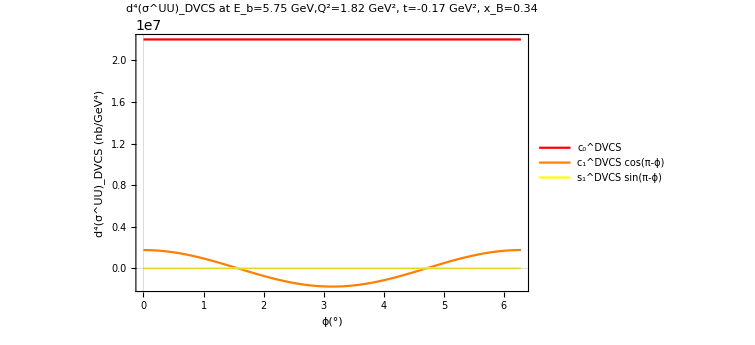

```mathematica
Plot[
{
ConvertGeVMinus6ToNbGevMinus4[
cODVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]
],
ConvertGeVMinus6ToNbGevMinus4[
c1DVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[1(π-ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[s1DVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[1(π- ϕ)]
]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"c_0^DVCS",
"c_1^DVCS cos(π-ϕ)",
"s_1^DVCS sin(π-ϕ)"
}
],
{0.85,0.75}
],
PlotStyle->{Red, Orange, Yellow},
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS (nb/GeV^4)"},
PlotLabel->"d^4(σ^UU)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific",
PlotRange->All
]
```

```mathematica
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))(1/(y^2 qSquared))cODVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]]
```

(0.00873903-8.23731×10^-22 ⅈ) nb/GeV^4

## (#4.3): Interference:

### (#4.3.1): Propagator 1, 𝒫_1(ϕ):

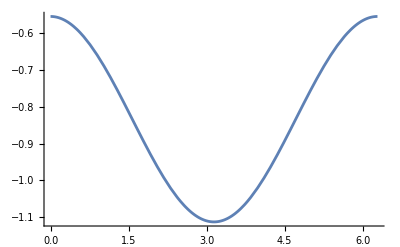

```mathematica
Propagator1[qSquared_,xB_,t_,ϕ_,ϵ_,y_,K_]:=(qSquared+2(((-qSquared)/(2y(1+ϵ^2)))(1+2 K Cos[π-ϕ]-(t/qSquared)(1-xB(2-y)+(y ϵ^2)/2)+(y ϵ^2)/2)))/qSquared;

Plot[Propagator1[qSquared,xB,t,ϕ,ϵ,y,K],{ϕ,0,2π}]
```

### (#4.3.2): Propagator 2, 𝒫_2(ϕ):

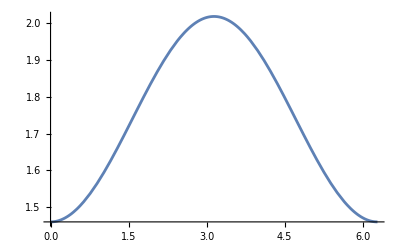

```mathematica
Propagator2[qSquared_,xB_,t_,ϕ_,ϵ_,y_,K_]:=(-2(((-qSquared)/(2y(1+ϵ^2)))(1+2 K Cos[π-ϕ]-(t/qSquared)(1-xB(2-y)+(y ϵ^2)/2)+(y ϵ^2)/2))+t)/qSquared;

Plot[Propagator2[qSquared,xB,t,ϕ,ϵ,y,K],{ϕ,0,2π}]
```

### (#4.3.3): Interference Contribution, ℐ:

#### (#4.3.3.1): Interference Contribution Function:

```mathematica
InterferenceContribution[λ_,Λ_,qSquared_,xB_,t_,ϕ_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=
(1/(xB t y^3 Propagator1[qSquared,xB,t,ϕ,ϵ,y,K]Propagator2[qSquared,xB,t,ϕ,ϵ,y,K]))*(
cOI[λ,Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]+
c1I[λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[1(π- ϕ)]+
c2I[λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[2(π-ϕ)]+
c3I[λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]Cos[3(π-ϕ)]+
s1I[λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[1(π-ϕ)]+
s2I[λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[2(π-ϕ)]+
s3I[Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[3(π-ϕ)]) ;
```

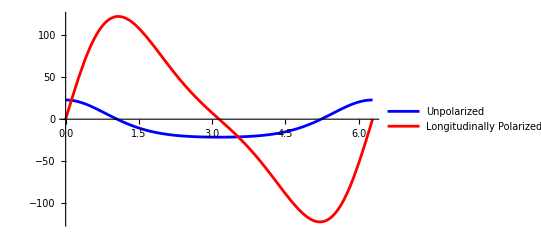

```mathematica
Plot[{1/2(InterferenceContribution[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT] ),
1/2(InterferenceContribution[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT] )},
{ϕ,0,2π},
PlotStyle->{Blue,Red},
PlotLegends->{"Unpolarized","Longitudinally Polarized"}]
```

#### (#4.3.3.2): Plot of Propagator 1, 𝒫_1(ϕ):

```mathematica
(* Here is a plot of the first Lepton Propagator *)
Plot[Propagator1[qSquared,xB,t,ϕ,ϵ,y,K],{ϕ,0,2π}]
```

-Graphics-

#### (#4.3.3.3): Plot of Propagator 2, 𝒫_2(ϕ):

```mathematica
(* Here is a plot of the second Lepton Propagator *)
Plot[Propagator2[qSquared,xB,t,ϕ,ϵ,y,K],{ϕ,0,2π}]
```

-Graphics-

#### (#4.3.3.4): Plot of (+) Helicity Beam and Unpolarized Target:

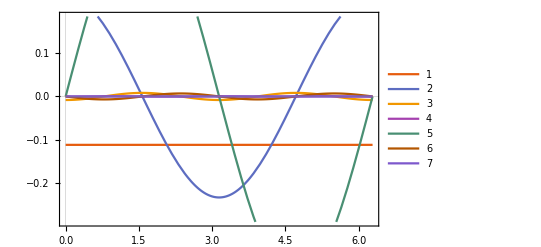

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the (+) Lepton Helicity beam*)
Plot[{
cOI[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
c1I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-1 ϕ],
c2I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-2ϕ],
c3I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]Cos[π-3ϕ],
s1I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-1 ϕ],
s2I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-2ϕ],
s3I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-3ϕ]
},
{ϕ,0,2π},
PlotLegends->Automatic,
PlotTheme->"Scientific"]
```

#### (#4.3.3.4): Plot of (+) Helicity Beam and LP Target:

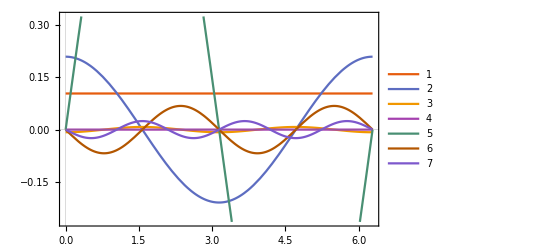

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the (+) Lepton Helicity beam*)
Plot[{
cOI[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
c1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-1 ϕ],
c2I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-2ϕ],
c3I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]Cos[π-3ϕ],
s1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-1 ϕ],
s2I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-2ϕ],
s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-3ϕ]
},
{ϕ,0,2π},
PlotLegends->Automatic,
PlotTheme->"Scientific"]
```

#### (#4.3.3.5): Plot of (-) Helicity Beam and Unpolarized Target:

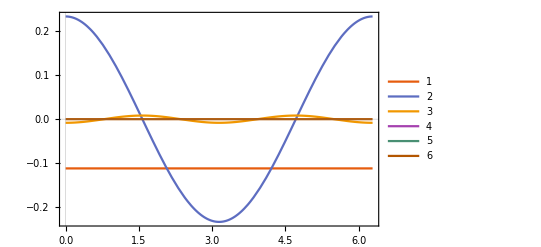

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the (-) Lepton Helicity beam*)
Plot[{
cOI[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
c1I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-1 ϕ],
c2I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-2ϕ],
s1I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-1 ϕ],
s2I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-2ϕ],
s3I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-3ϕ]
},
{ϕ,0,2π},
PlotLegends->Automatic,
PlotTheme->"Scientific"]
```

#### (#4.3.3.5): Plot of (-) Helicity Beam and LP Target:

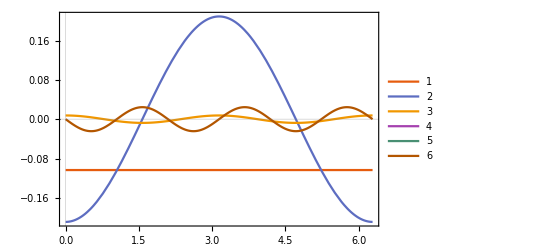

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the (-) Lepton Helicity beam*)
Plot[{
cOI[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
c1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-1 ϕ],
c2I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-2ϕ],
s1I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-1 ϕ],
s2I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-2ϕ],
s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-3ϕ]
},
{ϕ,0,2π},
PlotLegends->Automatic,
PlotTheme->"Scientific"]
```

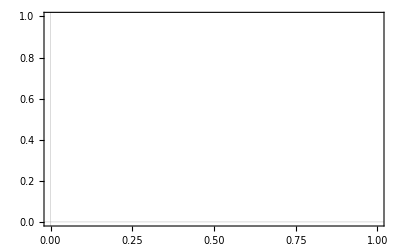

```mathematica
Plot[
cOI[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+
c1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-1 ϕ]+
c2I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-2ϕ]+
s1I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-1 ϕ]+
s2I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-2ϕ]+
s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-3ϕ],
{ϕ,0,2π},
PlotLegends->Automatic,
PlotTheme->"Scientific"]
```

```mathematica
Plot[
(1/(xB t y^3 Propagator1[qSquared,xB,t,ϕ,ϵ,y,K]Propagator2[qSquared,xB,t,ϕ,ϵ,y,K]))*(cOI[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+
c1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-1 ϕ]+
c2I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-2ϕ]+
s1I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-1 ϕ]+
s2I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-2ϕ]+
s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-3ϕ]),
{ϕ,0,2π},
PlotLegends->Automatic,
PlotTheme->"Scientific"]
```

-Graphics-

#### (#4.3.3.6): Plot of Unpolarized Helicity Beam and LP Target:

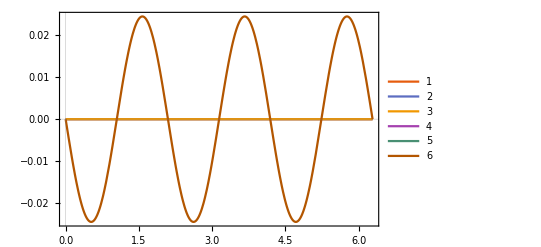

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the *unpolarized* Lepton Helicity beam*)
Plot[
{
(1/2)(cOI[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+cOI[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]),
(1/2)(c1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[1(π- ϕ)]+c1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[1(π- ϕ)]),
(1/2)(c2I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[2(π- ϕ)]+c2I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[2(π- ϕ)]),
(1/2)(s1I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[1(π- ϕ)]+s1I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[1(π- ϕ)]),
(1/2)(s2I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[2(π- ϕ)]+s2I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[2(π- ϕ)]),
(1/2)(s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[3(π- ϕ)]+s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[3(π- ϕ)])
},
{ϕ,0,2π},
PlotLegends->Automatic,
PlotTheme->"Scientific",
PlotRange->All]
```

## (#5): Cross Section: σ^XY | X = beam polarization, Y = target polarization

```mathematica
BKM10CrossSection[λ_,Λ_,qSquared_,xB_,t_,ϕ_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))(0 *BHContribution[]+DVCSContribution[λ,Λ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[λ,Λ,qSquared,xB,t,ϕ,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT])
];
```

## (#4.4.1): σ^UU | Unpolarized Beam, Unpolarized Target

### (#4.4.1.1): σ^UU | Unpolarized Beam, Unpolarized Target

#### (#4.4.1.1.1): Pure DVCS | σ^UU

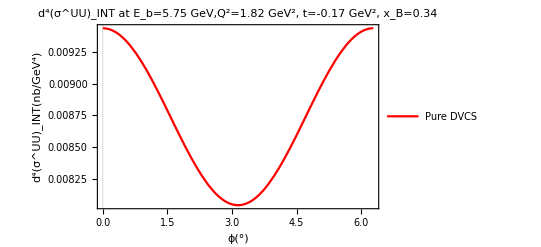

```mathematica
Plot[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2*(DVCSContribution[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^UU)_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^UU)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

#### (#4.4.1.1.2): Pure Interference | σ^UU

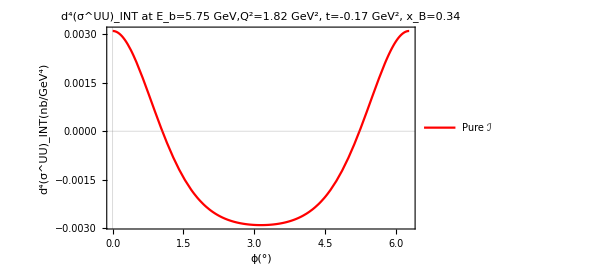

```mathematica
Plot[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure ℐ"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^UU)_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^UU)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

#### (#4.4.1.1.3): Total Cross Section | σ^UU

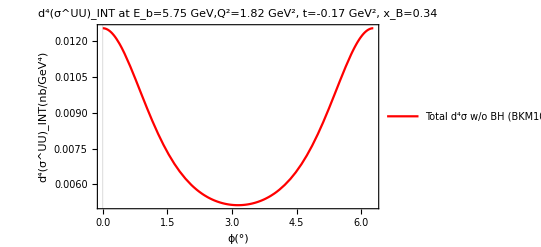

```mathematica
Plot[
1/2(BKM10CrossSection[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]),
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Total d^4σ w/o BH (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^UU)_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^UU)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

## (#4.4.2): σ^UL | Polarized Beam, Unpolarized Target

### (#4.4.2.1): σ^(U+) | (+) Polarized Beam, Unpolarized Target

#### (#4.4.2.1.1): Pure DVCS | σ^(U+)

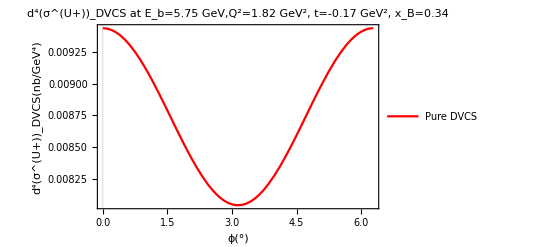

```mathematica
Plot[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
DVCSContribution[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^(U+))_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^(U+))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

#### (#4.4.2.1.2): Pure Interference | σ^(U+)

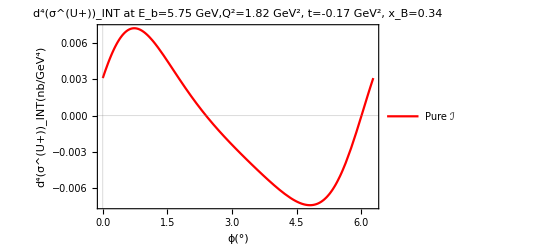

```mathematica
Plot[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure ℐ"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^(U+))_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^(U+))_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

#### (#4.4.2.1.3): Total Cross Section | σ^(U+)

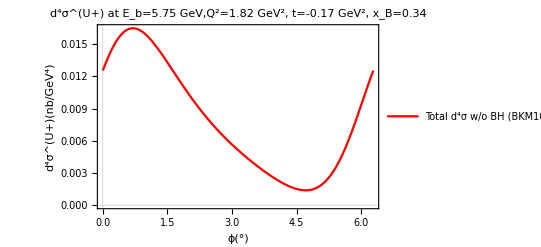

```mathematica
Plot[BKM10CrossSection[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Total d^4σ w/o BH (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4σ^(U+)(nb/GeV^4)"},
PlotLabel->"d^4σ^(U+) at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

### (#4.4.2.2): σ^(U-) | (-) Polarized Beam, Unpolarized Target

#### (#4.4.2.2.1): Pure DVCS | σ^(U-)

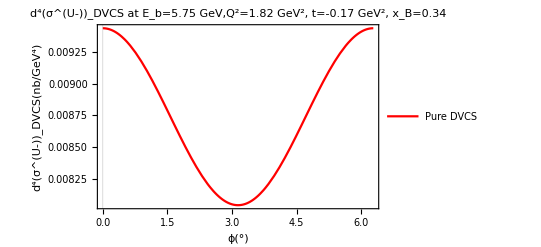

```mathematica
Plot[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^(U-))_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^(U-))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

#### (#4.4.2.2.2): Pure Interference | σ^(U-)

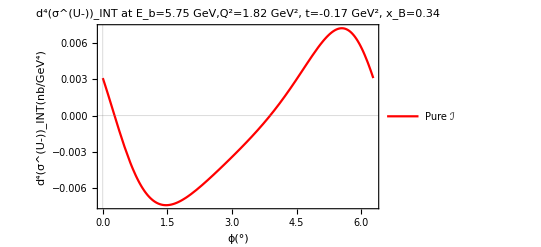

```mathematica
Plot[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure ℐ"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^(U-))_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^(U-))_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

#### (#4.4.2.2.3): Total Cross Section | σ^(U-)

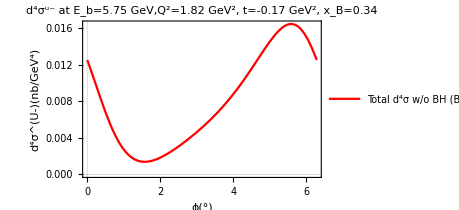

```mathematica
Plot[
BKM10CrossSection[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Total d^4σ w/o BH (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4σ^(U-)(nb/GeV^4)"},
PlotLabel->"d^4σ^(u-) at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

## (#4.4.3): σ^LU | Unpolarized Beam, Polarized Target

### (#4.4.3.1): σ^LU | Unpolarized Beam, Longitudinally-Polarized Target

#### (#4.4.3.1.1): Pure DVCS | σ^LU

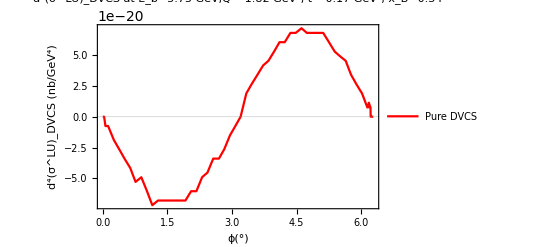

```mathematica
Plot[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2(DVCSContribution[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
],

{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^LU)_DVCS (nb/GeV^4)"},
PlotLabel->"d^4(σ^LU)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

#### (#4.4.3.1.2): Pure Interference | σ^LU

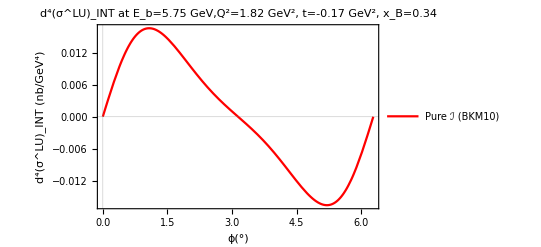

```mathematica
Plot[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure ℐ (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^LU)_INT (nb/GeV^4)"},
PlotLabel->"d^4(σ^LU)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

#### (#4.4.3.3.1): Total Cross Section | σ^LU

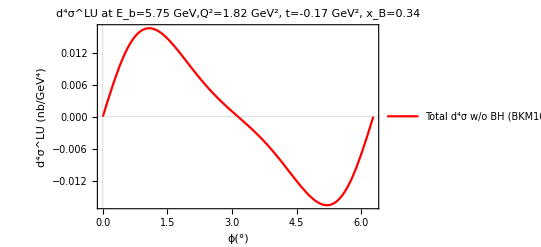

```mathematica
Plot[
1/2(BKM10CrossSection[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]),
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Total d^4σ w/o BH (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4σ^LU (nb/GeV^4)"},
PlotLabel->"d^4σ^LU at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

## (#4.4.4): σ^LL | Polarized Beam, Polarized Target

### (#4.4.4.1): σ^(L+) | Polarized Target, (+) Polarized Beam

#### (#4.4.4.1.1): Pure DVCS | σ^(L+)

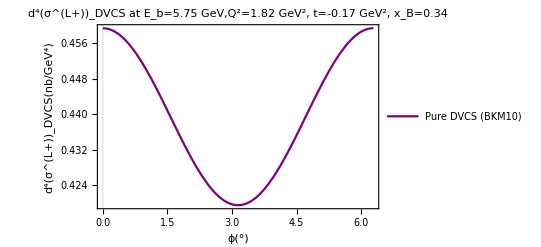

```mathematica
Plot[
DVCSContribution[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red, Blue, Purple},
FrameLabel->{"ϕ(°)","d^4(σ^(L+))_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^(L+))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

#### (#4.4.4.1.2): Pure Interference | σ^(L+)

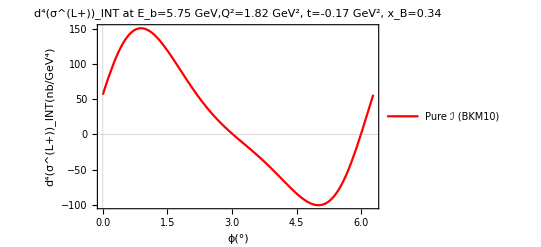

```mathematica
Plot[InterferenceContribution[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure ℐ (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^(L+))_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^(L+))_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

#### (#4.4.4.1.3): Combined | σ^(L+)

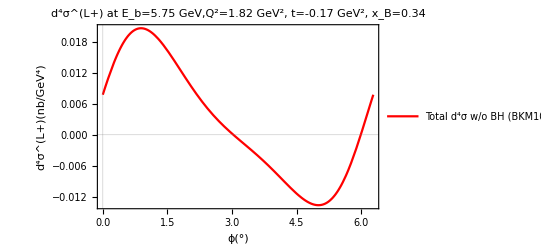

```mathematica
Plot[
BKM10CrossSection[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
,
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Total d^4σ w/o BH (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4σ^(L+)(nb/GeV^4)"},
PlotLabel->"d^4σ^(L+) at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

### (#4.4.4.2): σ^(L-) | Polarized Target, (-) Polarized Beam

#### (#4.4.4.2.1): Pure DVCS | σ^(L-)

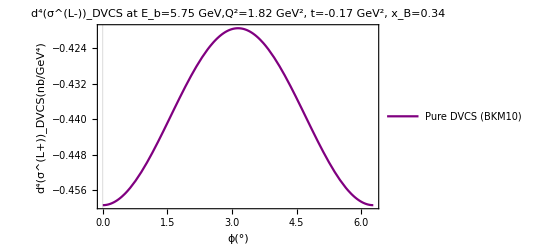

```mathematica
Plot[
DVCSContribution[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red, Blue, Purple},
FrameLabel->{"ϕ(°)","d^4(σ^(L+))_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^(L-))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

#### (#4.4.4.2.2): Pure Interference | σ^(L-)

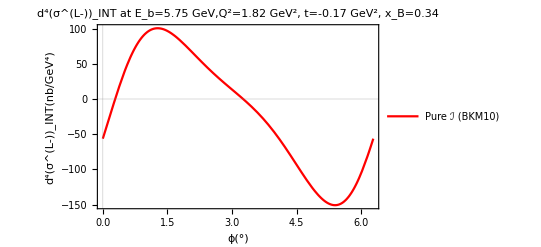

```mathematica
Plot[InterferenceContribution[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Pure ℐ (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^(L-))_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^(L-))_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

#### (#4.4.4.2.3): Combined | σ^(L-)

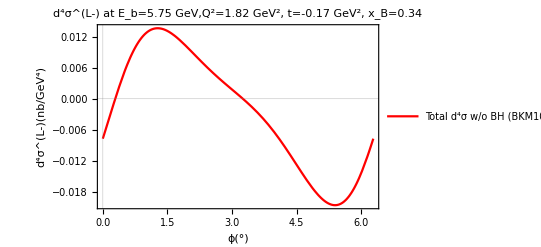

```mathematica
Plot[
BKM10CrossSection[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
,
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"Total d^4σ w/o BH (BKM10)"
}
],
{0.85,0.85}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4σ^(L-)(nb/GeV^4)"},
PlotLabel->"d^4σ^(L-) at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"]
```

## (#X): Testing:

## (#X.1): Cross-Checking c_2^ℐ:

Define the variables in question.

```mathematica
cpp=0.002414077755645961;
c0p=-0.21172805503862407;
curlyCpp=-57.8406742181105;
curlyC0p=1.9568253283721;
```

Try the individual product:

```mathematica
cpp*curlyCpp
c0p*curlyC0p
```

-0.139632

-0.414315

So the sum must be:

```mathematica
cpp*curlyCpp+c0p*curlyC0p
```

-0.553947

In conclusion, the Mathematica function is probably getting the wrong arguments.

## (#X.2): Cross-Checking s_2^ℐ:

First of all, Python is probably correct here...

The individual pieces are:

```mathematica
spp=0.004810462931411953;
s0p=0.5860907929841134;
curlySpp=-20.177953752886854;
curlyS0p=0.729452642853709;
```

Individual products are:

```mathematica
spp*curlySpp
s0p*curlyS0p
```

-0.0970653

0.427525

The sum is:

```mathematica
spp*curlySpp+s0p*curlyS0p
```

0.33046

Python gives 0.3304601793344807.

There is also one more possibility:

```mathematica
(0.004810462931411953*-20.177953752886854)+(0.5860907929841134*0.729452642853709)
```

0.33046

## (#X.3): Testing Amplitude Squared Prefactor:

```mathematica
(ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2))
```

3.49442×10^-10 /GeV^4

## (#X.4): Understanding “Associations” in Mathematica:

```mathematica
(*Step 1:Define the functions and their arguments*)
functions=<|
"(C^unp)_(++)(n=0)"->CunpPP0,
"(C^unp)_(++)(n=1)"->CunpPP1,
"(C^unp)_(++)(n=2)"->CunpPP2,
"(C^unp)_(++)(n=3)"->CunpPP3,
"(C^(unp, V))_(++)(n=0)"->CunpVPP0,
"(C^(unp, V))_(++)(n=1)"->CunpVPP1,
"(C^(unp, V))_(++)(n=2)"->CunpVPP2,
"(C^(unp, V))_(++)(n=3)"->CunpVPP3,
"(C^(unp, A))_(++)(n=0)"->CunpAPP0,
"(C^(unp, A))_(++)(n=1)"->CunpAPP1,
"(C^(unp, A))_(++)(n=2)"->CunpAPP2,
"(C^(unp, A))_(++)(n=3)"->CunpAPP3,
"(C^unp)_(0+)(n=0)"->Cunp0P0,
"(C^unp)_(0+)(n=1)"->Cunp0P1,
"(C^unp)_(0+)(n=2)"->Cunp0P2,
"(C^(unp, V))_(0+)(n=0)"->Cunp0P0V,
"(C^(unp, V))_(0+)(n=1)"->Cunp0P1V,
"(C^(unp, V))_(0+)(n=2)"->Cunp0P2V,
"(C^(unp, A))_(0+)(n=0)"->Cunp0P0A,
"(C^(unp, A))_(0+)(n=1)"->Cunp0P1A,
"(C^(unp, A))_(0+)(n=2)"->Cunp0P2A
|>;
```

```mathematica
arguments=<|
"(C^unp)_(++)(n=0)"->{qSquared,xB,t,ϵ,y,kT},
"(C^unp)_(++)(n=1)"->{qSquared,xB,t,ϵ,y,K},
"(C^unp)_(++)(n=2)"->{qSquared,xB,t,ϵ,y,tP,kT},
"(C^unp)_(++)(n=3)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, V))_(++)(n=0)"->{qSquared,xB,t,ϵ,y,kT},
"(C^(unp, V))_(++)(n=1)"->{qSquared,xB,t,ϵ,y,tP,K},
"(C^(unp, V))_(++)(n=2)"->{qSquared,xB,t,ϵ,y,tP,kT},
"(C^(unp, V))_(++)(n=3)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, A))_(++)(n=0)"->{qSquared,xB,t,ϵ,y,kT},
"(C^(unp, A))_(++)(n=1)"->{qSquared,xB,t,ϵ,y,tP,K},
"(C^(unp, A))_(++)(n=2)"->{qSquared,xB,t,ϵ,y,tP,kT},
"(C^(unp, A))_(++)(n=3)"->{qSquared,xB,t,ϵ,y,tP,K},
"(C^unp)_(0+)(n=0)"->{qSquared,xB,t,ϵ,y,K},
"(C^unp)_(0+)(n=1)"->{qSquared,xB,t,ϵ,y,tP},
"(C^unp)_(0+)(n=2)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, V))_(0+)(n=0)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, V))_(0+)(n=1)"->{qSquared,xB,t,ϵ,y,kT},
"(C^(unp, V))_(0+)(n=2)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, A))_(0+)(n=0)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, A))_(0+)(n=1)"->{qSquared,xB,t,ϵ,y,kT},
"(C^(unp, A))_(0+)(n=2)"->{qSquared,xB,t,ϵ,y,tP,K}
|>;
```

```mathematica
(*Step 2:Evaluate each function with its corresponding arguments*)
results=Table[
functions[key]@@arguments[key],
{key,Keys[functions]}
];
```

```mathematica
(*Step 3:Create labels for each function*)
labels=Keys[functions]
```

{(C^unp)_(++)(n=0),(C^unp)_(++)(n=1),(C^unp)_(++)(n=2),(C^unp)_(++)(n=3),(C^(unp, V))_(++)(n=0),(C^(unp, V))_(++)(n=1),(C^(unp, V))_(++)(n=2),(C^(unp, V))_(++)(n=3),(C^(unp, A))_(++)(n=0),(C^(unp, A))_(++)(n=1),(C^(unp, A))_(++)(n=2),(C^(unp, A))_(++)(n=3),(C^unp)_(0+)(n=0),(C^unp)_(0+)(n=1),(C^unp)_(0+)(n=2),(C^(unp, V))_(0+)(n=0),(C^(unp, V))_(0+)(n=1),(C^(unp, V))_(0+)(n=2),(C^(unp, A))_(0+)(n=0),(C^(unp, A))_(0+)(n=1),(C^(unp, A))_(0+)(n=2)}

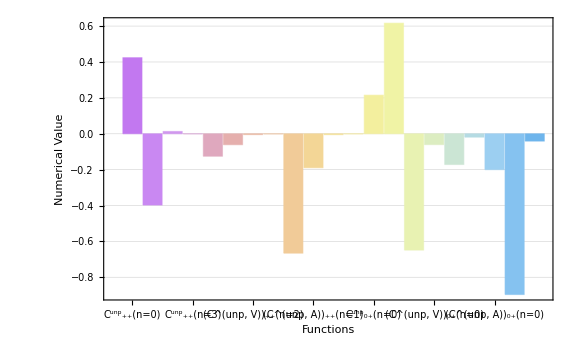

```mathematica
(*Step 4:Generate the bar chart*)
BarChart[
results,
ChartLabels->labels,
BarSpacing->0.05,
PlotTheme->"Detailed",
ChartStyle->"Pastel",
LabelStyle->Directive[Bold,FontSize->6],
RotateLabel->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
Frame->True,
AxesOrigin->{0,0},
FrameLabel->{"Functions","Numerical Value"},
ImageSize->Large
]
```